```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\Tools\Scripts

```mathematica
(*Absorbing Markov Chain with 1 absorbing end state, 1 partially reflecting state and 4 transition states*)
```

```mathematica
Q=({{0, 0.5, 0, 0, 0}, {0.5, 0, 0.5, 0, 0}, {0, 0.5, 0, 0.5, 0}, {0, 0, 0.5, 0, 0.5}, {0, 0, 0, 0.5, 0.5}});
```

```mathematica
R=({{0.5}, {0}, {0}, {0}, {0}});
```

```mathematica
I5=IdentityMatrix[5];
```

```mathematica
F=Inverse[I5-Q];
```

```mathematica
MatrixForm[F]
```

(2. | 2. | 2. | 2. | 2.
2. | 4. | 4. | 4. | 4.
2. | 4. | 6. | 6. | 6.
2. | 4. | 6. | 8. | 8.
2. | 4. | 6. | 8. | 10.)

```mathematica
MatrixForm[Total[F]]
```

(10.
18.
24.
28.
30.)

```mathematica
calctau[n_,ToRef_]:=
Module[{},
QMat=Append[(IdentityMatrix[n]/2)[[2;;-1]],Table[0,{n}]]+Join[{Table[0,{n}]},(IdentityMatrix[n]/2)[[1;;-2]]];
QMat[[-1,-1]]=1/2;
RMat=Join[{0.5},Table[0,{n-1}]];
IMat=IdentityMatrix[n];
FMat=Inverse[IMat-QMat];
TauMat=Total[FMat];
TauMat[[-ToRef]]
];
```

```mathematica
(*Convergence with ToRef
Example case: 
Ag100: z_absorb = 0, z_ini = 60, z_partial_reflect = z_ini + ToRef
Ag111: z_absorb = 0, z_ini = 30, z_partial_reflect = z_ini + ToRef
*)
```

```mathematica
ToRefList=Range[11,511,20];
pratio=Reap[
For[i=1,i≤Length[ToRefList],i++,
top=calctau[59+ToRefList[[i]],ToRefList[[i]]];
bot=calctau[29+ToRefList[[i]],ToRefList[[i]]];
Sow[N[top/bot]];
]
][[2,1]];
```

```mathematica
pratio
```

{3.17647,2.65934,2.45802,2.35088,2.28436,2.23904,2.20619,2.18127,2.16173,2.14599,2.13304,2.1222,2.11299,2.10508,2.0982,2.09217,2.08683,2.08208,2.07782,2.07398,2.07051,2.06734,2.06445,2.06179,2.05935,2.05709}

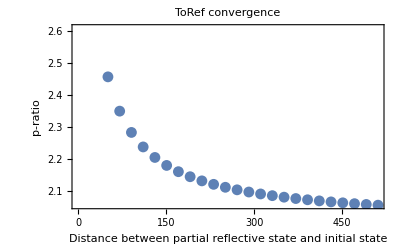

```mathematica
ListPlot[Partition[Riffle[Range[11,511,20],pratio],2],Frame->True,PlotLabel->"ToRef convergence",FrameLabel->{"Distance between partial reflective state and initial state","p-ratio"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
(*Convergence with resolution
Example case: 
Ag100: z_absorb = 0 Ang, z_ini = 6 Ang, z_partial_reflect = z_ini + ToRef
Ag111: z_absorb = 0 Ang, z_ini = 3 Ang, z_partial_reflect = z_ini + ToRef
ToRef = 230
*)
```

```mathematica
ToRefList={24,231,461};
ntopList={29,290,580};
nbotList={26,260,520};
pratioRes=Reap[
For[i=1,i≤Length[ToRefList],i++,
top=calctau[ntopList[[i]],ToRefList[[i]]];
bot=calctau[nbotList[[i]],ToRefList[[i]]];
Sow[N[top/bot]];
]
][[2,1]];
```

```mathematica
pratioRes
```

{2.12,2.1222,2.12232}

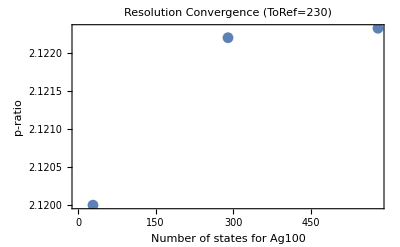

```mathematica
ListPlot[Partition[Riffle[ntopList,pratioRes],2],Frame->True,PlotLabel->"Resolution Convergence (ToRef=230)",FrameLabel->{"Number of states for Ag100","p-ratio"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
(*Variation with difference of the z_ini (thus the dropping length difference from the PVP/ Agsurface)
Ag100: z_absorb = 0, z_ini = 60, z_partial_reflect = z_ini + 231
Ag111: z_absorb = 0, z_ini = vary, z_partial_reflect = z_ini + 231
ToRef = 230
*)
```

```mathematica
nbotVary={9,19,29,39,49,59};
prationbot=Reap[
For[i=1,i≤Length[nbotVary],i++,
top=calctau[290,231];
bot=calctau[nbotVary[[i]]+231,231];
Sow[N[top/bot]];
]
][[2,1]];
```

```mathematica
prationbot
```

{6.63694,3.24948,2.1222,1.55988,1.22348,1.}

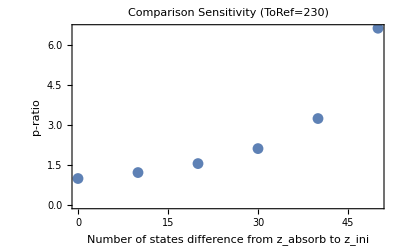

```mathematica
ListPlot[Partition[Riffle[59-nbotVary,prationbot],2],Frame->True,
PlotLabel->"Comparison Sensitivity (ToRef=230)",FrameLabel->{"Number of states difference from z_absorb to z_ini","p-ratio"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
(* Applying to Flux PMF Xin PVP10
z-absorb: Ag100 = 20.7875 Ang, Ag111 = 23.4625 Ang
  Difference = 2.675 Ang
Divide difference into 50 states
1 Markov state = 0.0535 Ang
*)
```

```mathematica
zdiff=50;
```

```mathematica
(*ToRef Convergence
Set initial state to be 20 states above Ag111 absorbing state = 1.07 Ang
*)
```

```mathematica
ToRefList=Range[11,1011,50];
pratio=Reap[
For[i=1,i≤Length[ToRefList],i++,
top=calctau[19+zdiff+ToRefList[[i]],ToRefList[[i]]];
bot=calctau[19+ToRefList[[i]],ToRefList[[i]]];
Sow[N[top/bot]];
]
][[2,1]];
```

$Aborted

```mathematica
pratio
```

{7.76829,4.74113,4.22614,4.0132,3.89683,3.82348,3.77301,3.73617,3.70809,3.68597,3.66811,3.65337,3.64102,3.6305,3.62144,3.61356,3.60664,3.60052,3.59506,3.59016,3.58574}

```mathematica
ToRefList=Range[11,1011,50];
pratio={7.7682926829268295,4.74113475177305,4.226141078838174,4.013196480938417,3.8968253968253967,3.8234750462107208,3.7730109204368176,3.7361673414304994,3.7080856123662307,3.685972369819341,3.6681075888568686,3.6533742331288344,3.6410153102336826,3.6304996271439225,3.621443442054129,3.6135626216742374,3.606642291285801,3.6005169442848937,3.5950570342205324,3.590159711488923,3.5857422831945125}
```

{7.76829,4.74113,4.22614,4.0132,3.89683,3.82348,3.77301,3.73617,3.70809,3.68597,3.66811,3.65337,3.64102,3.6305,3.62144,3.61356,3.60664,3.60052,3.59506,3.59016,3.58574}

```mathematica
100*(pratio[[7]]-pratio[[-1]])/pratio[[-1]]
```

5.22259

```mathematica
ToRefList[[7]]
```

311

```mathematica
ToRefList[[7]]*0.0535
```

16.6385

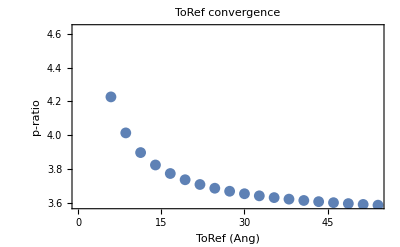

```mathematica
ToRefConv=ListPlot[Partition[Riffle[ToRefList*0.0535,pratio],2],Frame->True,PlotLabel->"ToRef convergence",FrameLabel->{"ToRef (Ang)","p-ratio"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
CreateDirectory["graphs"];
Export["graphs/ToRef-Convergence.png",ToRefConv,ImageResolution->100];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\Tools\\Scripts\\graphs\\" already exists.

```mathematica
(*Convergence with resolution
ToRef = 311
*)
```

```mathematica
ToRefList={32,311,621};
ntopList={38,380,760};
nbotList={33,330,660};
pratioRes=Reap[
For[i=1,i≤Length[ToRefList],i++,
top=calctau[ntopList[[i]],ToRefList[[i]]];
bot=calctau[nbotList[[i]],ToRefList[[i]]];
Sow[N[top/bot]];
]
][[2,1]];
```

```mathematica
pratioRes
```

{3.76923,3.77301,3.77322}

```mathematica
100*(pratioRes[[3]]-pratioRes[[2]])/pratioRes[[3]]
```

0.00564831

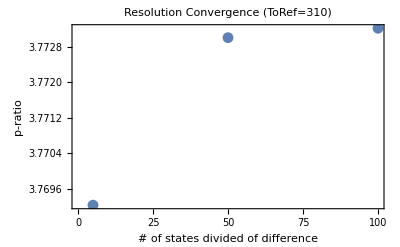

```mathematica
ResConv=ListPlot[Partition[Riffle[{5,50,100},pratioRes],2],Frame->True,PlotLabel->"Resolution Convergence (ToRef=310)",FrameLabel->{"# of states divided of difference","p-ratio"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
Export["graphs/Resolution-Convergence.png",ResConv,ImageResolution->100];
```

```mathematica
(*Vary z_ini
ToRef=311
*)
```

```mathematica
ziniVary=Range[1,101,5];
prationbot=Reap[
For[i=1,i≤Length[ziniVary],i++,
top=calctau[ziniVary[[i]]+zdiff+311,311];
bot=calctau[ziniVary[[i]]+311,311];
Sow[N[top/bot]];
]
][[2,1]];
```

```mathematica
prationbot
```

{28.0867,8.79117,5.57478,4.25005,3.52722,3.0719,2.75871,2.53003,2.35567,2.21831,2.10727,2.01563,1.9387,1.87318,1.8167,1.7675,1.72425,1.68592,1.65172,1.621,1.59325}

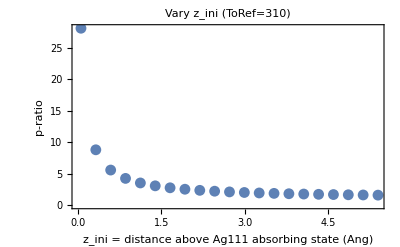

```mathematica
ziniGraph=ListPlot[Partition[Riffle[ziniVary*0.0535,prationbot],2],Frame->True,
PlotLabel->"Vary z_ini (ToRef=310)",FrameLabel->{"z_ini = distance above Ag111 absorbing state (Ang)","p-ratio"},PlotRange->All,LabelStyle->Directive[FontSize->15]]
```

```mathematica
Export["graphs/ziniGraph-Ref.png",ziniGraph,ImageResolution->100]
```

graphs/ziniGraph-Ref.png

```mathematica
(*Vary z_diff
ToRef=311
z_ini=41
*)
```

```mathematica
zdiffVary=Range[1,201,20];
prationzdiff=Reap[
For[i=1,i≤Length[zdiffVary],i++,
top=calctau[41+zdiffVary[[i]]+311,311];
bot=calctau[41+311,311];
Sow[N[top/bot]];
]
][[2,1]];
```

```mathematica
prationzdiff
```

{1.02535,1.54751,2.0984,2.67801,3.28636,3.92344,4.58924,5.28378,6.00704,6.75903,7.53975}

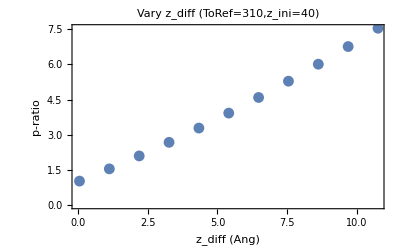

```mathematica
zdiffGraph=ListPlot[Partition[Riffle[zdiffVary*0.0535,prationzdiff],2],Frame->True,
PlotLabel->"Vary z_diff (ToRef=310,z_ini=40)",FrameLabel->{"z_diff (Ang)","p-ratio"},PlotRange->All,LabelStyle->Directive[FontSize->15]]
```

```mathematica
Export["graphs/zdiffGraph-Ref.png",zdiffGraph,ImageResolution->100]
```

graphs/zdiffGraph-Ref.png

```mathematica
top=calctau[31+50+231,231];
bot=calctau[31+231,231];
```

```mathematica
N[top/bot]
```

2.82239